```mathematica
SetDirectory["/home/kn/Documents/thesis"]
```

/home/kn/Documents/thesis

```mathematica
data = Import["XBTUSD-5m-data.csv",{"Data",All,6}]
data = Delete[data, 1]
```

{close,9499.5,9498.5,9493.,9511.,9498.,9498.5,9507.,9488.,9499.5,9494.5,9492.5,9487.5,9489.5,9480.5,9477.5,9478.5,9487.,9484.,52955,8596.,8607.,8601.,8605.5,8610.,8627.,8619.,8621.5,8616.5,8625.,8623.,8624.5,8624.,8638.,8646.5,8626.,8624.,8625.,8620.}
 |  |  |  |

{9499.5,9498.5,9493.,9511.,9498.,9498.5,9507.,9488.,9499.5,9494.5,9492.5,9487.5,9489.5,9480.5,9477.5,9478.5,9487.,9484.,9475.5,52954,8596.,8607.,8601.,8605.5,8610.,8627.,8619.,8621.5,8616.5,8625.,8623.,8624.5,8624.,8638.,8646.5,8626.,8624.,8625.,8620.}
 |  |  |  |

```mathematica
ClearAll[x, y, σ, θ, κ, β, τ]
```

```mathematica
lPdf = Log[σ*y^β] + 1/(2*τ) * ((x^(2-2β) - 2x^(1-β)*y^(1-β) + y^(2-2β))/(σ^2*(1-2β + β^2)) -τ*(x^(1-β) - y^(1-β))*(2*κ*θ-2*κ*y-σ^2*β*y^(2β-1))/(σ^2*(1-β)*y^β) + τ^2*(4*κ^2*θ^2 - 8*κ^2*θ*y+4κ^2*y^2 - 4*κ*θ*σ^2*β*y^(2*β-1)+4*κ*σ^2*β*y^(2*β) + σ^4*β^2*y^(4*β-2))/(4*σ^2*y^(2*β)))- Log[1/Sqrt[2*Pi*τ]]
```

1/(2 τ)((x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β))/((1-2 β+β^2) σ^2)-(y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β) σ^2)+(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2)/(4 σ^2))+Log[y^β σ]-Log[1/(√(2 π) √τ)]

0.5

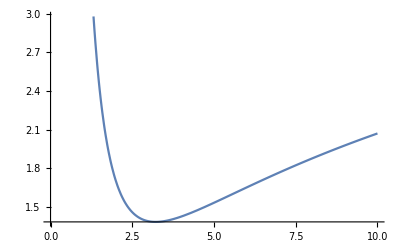

```mathematica
θ = Mean[data];
x = data[[2]];
y = data[[1]];
κ = 5;
β = 0.5
τ = 5/(365*24*60);
Plot[Log[σ*y^β] + 1/(2*τ) * ((x^(2-2β) - 2x^(1-β)*y^(1-β) + y^(2-2β))/(σ^2*(1-2β + β^2)) -τ*(x^(1-β) - y^(1-β))*(2*κ*θ-2*κ*y-σ^2*β*y^(2β-1))/(σ^2*(1-β)*y^β) + τ^2*(4*κ^2*θ^2 - 8*κ^2*θ*y+4κ^2*y^2 - 4*κ*θ*σ^2*β*y^(2*β-1)+4*κ*σ^2*β*y^(2*β) + σ^4*β^2*y^(4*β-2))/(4*σ^2*y^(2*β)))- Log[1/Sqrt[2*Pi*τ]], {σ, 0, 10}]
```

```mathematica
gradF = D[lPdf, {{σ, θ, κ, β}}]
hess = D[lPdf, {{σ, θ, κ, β}, 2}]
```

{1/σ+1/(2 τ)(-(2 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)))/((1-2 β+β^2) σ^3)+(2 y^(-1+β) (x^(1-β)-y^(1-β)) β τ)/((1-β) σ)+(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β) σ^3)+(y^(-2 β) (8 y^(2 β) β κ σ-8 y^(-1+2 β) β θ κ σ+4 y^(-2+4 β) β^2 σ^3) τ^2)/(4 σ^2)-(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2)/(2 σ^3)),(-(2 y^-β (x^(1-β)-y^(1-β)) κ τ)/((1-β) σ^2)+(y^(-2 β) (-8 y κ^2+8 θ κ^2-4 y^(-1+2 β) β κ σ^2) τ^2)/(4 σ^2))/(2 τ),(-(y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ)/((1-β) σ^2)+(y^(-2 β) (8 y^2 κ-16 y θ κ+8 θ^2 κ+4 y^(2 β) β σ^2-4 y^(-1+2 β) β θ σ^2) τ^2)/(4 σ^2))/(2 τ),Log[y]+1/(2 τ)(-((x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)) (-2+2 β))/((1-2 β+β^2)^2 σ^2)-(y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β)^2 σ^2)+(y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y])/((1-β) σ^2)-(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2 Log[y])/(2 σ^2)-(y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)+(-2 x^(2-2 β) Log[x]+2 x^(1-β) y^(1-β) Log[x]-2 y^(2-2 β) Log[y]+2 x^(1-β) y^(1-β) Log[y])/((1-2 β+β^2) σ^2)-(y^-β (x^(1-β)-y^(1-β)) τ (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β) σ^2)+1/(4 σ^2)y^(-2 β) τ^2 (4 y^(2 β) κ σ^2-4 y^(-1+2 β) θ κ σ^2+2 y^(-2+4 β) β σ^4+8 y^(2 β) β κ σ^2 Log[y]-8 y^(-1+2 β) β θ κ σ^2 Log[y]+4 y^(-2+4 β) β^2 σ^4 Log[y]))}

{{-1/σ^2+1/(2 τ)((6 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)))/((1-2 β+β^2) σ^4)-(6 y^(-1+β) (x^(1-β)-y^(1-β)) β τ)/((1-β) σ^2)-(6 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β) σ^4)+(y^(-2 β) (8 y^(2 β) β κ-8 y^(-1+2 β) β θ κ+12 y^(-2+4 β) β^2 σ^2) τ^2)/(4 σ^2)-(y^(-2 β) (8 y^(2 β) β κ σ-8 y^(-1+2 β) β θ κ σ+4 y^(-2+4 β) β^2 σ^3) τ^2)/σ^3+(3 y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2)/(2 σ^4)),((4 y^-β (x^(1-β)-y^(1-β)) κ τ)/((1-β) σ^3)-(2 β κ τ^2)/(y σ)-(y^(-2 β) (-8 y κ^2+8 θ κ^2-4 y^(-1+2 β) β κ σ^2) τ^2)/(2 σ^3))/(2 τ),1/(2 τ)((2 y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ)/((1-β) σ^3)+(y^(-2 β) (8 y^(2 β) β σ-8 y^(-1+2 β) β θ σ) τ^2)/(4 σ^2)-(y^(-2 β) (8 y^2 κ-16 y θ κ+8 θ^2 κ+4 y^(2 β) β σ^2-4 y^(-1+2 β) β θ σ^2) τ^2)/(2 σ^3)),1/(2 τ)((2 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)) (-2+2 β))/((1-2 β+β^2)^2 σ^3)+(2 y^(-1+β) (x^(1-β)-y^(1-β)) τ)/((1-β) σ)+(2 y^(-1+β) (x^(1-β)-y^(1-β)) β τ)/((1-β)^2 σ)+(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β)^2 σ^3)+(2 y^(-1+β) (x^(1-β)-y^(1-β)) β τ Log[y])/((1-β) σ)-(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y])/((1-β) σ^3)-(y^(-2 β) (8 y^(2 β) β κ σ-8 y^(-1+2 β) β θ κ σ+4 y^(-2+4 β) β^2 σ^3) τ^2 Log[y])/(2 σ^2)+(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2 Log[y])/σ^3+(2 y^(-1+β) β τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ)+(2 y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^3)-(2 (-2 x^(2-2 β) Log[x]+2 x^(1-β) y^(1-β) Log[x]-2 y^(2-2 β) Log[y]+2 x^(1-β) y^(1-β) Log[y]))/((1-2 β+β^2) σ^3)+(2 y^-β (x^(1-β)-y^(1-β)) τ (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β) σ^3)+1/(4 σ^2)y^(-2 β) τ^2 (8 y^(2 β) κ σ-8 y^(-1+2 β) θ κ σ+8 y^(-2+4 β) β σ^3+16 y^(2 β) β κ σ Log[y]-16 y^(-1+2 β) β θ κ σ Log[y]+16 y^(-2+4 β) β^2 σ^3 Log[y])-1/(2 σ^3)y^(-2 β) τ^2 (4 y^(2 β) κ σ^2-4 y^(-1+2 β) θ κ σ^2+2 y^(-2+4 β) β σ^4+8 y^(2 β) β κ σ^2 Log[y]-8 y^(-1+2 β) β θ κ σ^2 Log[y]+4 y^(-2+4 β) β^2 σ^4 Log[y]))},{((4 y^-β (x^(1-β)-y^(1-β)) κ τ)/((1-β) σ^3)-(2 β κ τ^2)/(y σ)-(y^(-2 β) (-8 y κ^2+8 θ κ^2-4 y^(-1+2 β) β κ σ^2) τ^2)/(2 σ^3))/(2 τ),(y^(-2 β) κ^2 τ)/σ^2,(-(2 y^-β (x^(1-β)-y^(1-β)) τ)/((1-β) σ^2)+(y^(-2 β) (-16 y κ+16 θ κ-4 y^(-1+2 β) β σ^2) τ^2)/(4 σ^2))/(2 τ),1/(2 τ)(-(2 y^-β (x^(1-β)-y^(1-β)) κ τ)/((1-β)^2 σ^2)+(2 y^-β (x^(1-β)-y^(1-β)) κ τ Log[y])/((1-β) σ^2)-(y^(-2 β) (-8 y κ^2+8 θ κ^2-4 y^(-1+2 β) β κ σ^2) τ^2 Log[y])/(2 σ^2)-(2 y^-β κ τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)+(y^(-2 β) τ^2 (-4 y^(-1+2 β) κ σ^2-8 y^(-1+2 β) β κ σ^2 Log[y]))/(4 σ^2))},{1/(2 τ)((2 y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ)/((1-β) σ^3)+(y^(-2 β) (8 y^(2 β) β σ-8 y^(-1+2 β) β θ σ) τ^2)/(4 σ^2)-(y^(-2 β) (8 y^2 κ-16 y θ κ+8 θ^2 κ+4 y^(2 β) β σ^2-4 y^(-1+2 β) β θ σ^2) τ^2)/(2 σ^3)),(-(2 y^-β (x^(1-β)-y^(1-β)) τ)/((1-β) σ^2)+(y^(-2 β) (-16 y κ+16 θ κ-4 y^(-1+2 β) β σ^2) τ^2)/(4 σ^2))/(2 τ),(y^(-2 β) (8 y^2-16 y θ+8 θ^2) τ)/(8 σ^2),1/(2 τ)(-(y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ)/((1-β)^2 σ^2)+(y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ Log[y])/((1-β) σ^2)-(y^(-2 β) (8 y^2 κ-16 y θ κ+8 θ^2 κ+4 y^(2 β) β σ^2-4 y^(-1+2 β) β θ σ^2) τ^2 Log[y])/(2 σ^2)-(y^-β (-2 y+2 θ) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)+(y^(-2 β) τ^2 (4 y^(2 β) σ^2-4 y^(-1+2 β) θ σ^2+8 y^(2 β) β σ^2 Log[y]-8 y^(-1+2 β) β θ σ^2 Log[y]))/(4 σ^2))},{1/(2 τ)((2 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)) (-2+2 β))/((1-2 β+β^2)^2 σ^3)+(2 y^(-1+β) (x^(1-β)-y^(1-β)) β τ)/((1-β)^2 σ)+(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β)^2 σ^3)-(2 y^(-1+β) (x^(1-β)-y^(1-β)) β τ Log[y])/((1-β) σ)-(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y])/((1-β) σ^3)-(y^(-2 β) (8 y^(2 β) β κ σ-8 y^(-1+2 β) β θ κ σ+4 y^(-2+4 β) β^2 σ^3) τ^2 Log[y])/(2 σ^2)+(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2 Log[y])/σ^3+(2 y^(-1+β) β τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ)+(2 y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^3)-(2 (-2 x^(2-2 β) Log[x]+2 x^(1-β) y^(1-β) Log[x]-2 y^(2-2 β) Log[y]+2 x^(1-β) y^(1-β) Log[y]))/((1-2 β+β^2) σ^3)-(y^-β (x^(1-β)-y^(1-β)) τ (-2 y^(-1+2 β) σ-4 y^(-1+2 β) β σ Log[y]))/((1-β) σ^2)+(2 y^-β (x^(1-β)-y^(1-β)) τ (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β) σ^3)+1/(4 σ^2)y^(-2 β) τ^2 (8 y^(2 β) κ σ-8 y^(-1+2 β) θ κ σ+8 y^(-2+4 β) β σ^3+16 y^(2 β) β κ σ Log[y]-16 y^(-1+2 β) β θ κ σ Log[y]+16 y^(-2+4 β) β^2 σ^3 Log[y])-1/(2 σ^3)y^(-2 β) τ^2 (4 y^(2 β) κ σ^2-4 y^(-1+2 β) θ κ σ^2+2 y^(-2+4 β) β σ^4+8 y^(2 β) β κ σ^2 Log[y]-8 y^(-1+2 β) β θ κ σ^2 Log[y]+4 y^(-2+4 β) β^2 σ^4 Log[y])),1/(2 τ)(-(2 y^-β (x^(1-β)-y^(1-β)) κ τ)/((1-β)^2 σ^2)+(2 y^-β (x^(1-β)-y^(1-β)) κ τ Log[y])/((1-β) σ^2)-(y^(-2 β) (-8 y κ^2+8 θ κ^2-4 y^(-1+2 β) β κ σ^2) τ^2 Log[y])/(2 σ^2)-(2 y^-β κ τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)+(y^(-2 β) τ^2 (-4 y^(-1+2 β) κ σ^2-8 y^(-1+2 β) β κ σ^2 Log[y]))/(4 σ^2)),1/(2 τ)(-(y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ)/((1-β)^2 σ^2)+(y^-β (x^(1-β)-y^(1-β)) (-2 y+2 θ) τ Log[y])/((1-β) σ^2)-(y^(-2 β) (8 y^2 κ-16 y θ κ+8 θ^2 κ+4 y^(2 β) β σ^2-4 y^(-1+2 β) β θ σ^2) τ^2 Log[y])/(2 σ^2)-(y^-β (-2 y+2 θ) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)+(y^(-2 β) τ^2 (4 y^(2 β) σ^2-4 y^(-1+2 β) θ σ^2+8 y^(2 β) β σ^2 Log[y]-8 y^(-1+2 β) β θ σ^2 Log[y]))/(4 σ^2)),1/(2 τ)((2 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)) (-2+2 β)^2)/((1-2 β+β^2)^3 σ^2)-(2 (x^(2-2 β)+y^(2-2 β)-2 x^(1-β) y^(1-β)))/((1-2 β+β^2)^2 σ^2)-(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ)/((1-β)^3 σ^2)+(2 y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y])/((1-β)^2 σ^2)-(y^-β (x^(1-β)-y^(1-β)) (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y]^2)/((1-β) σ^2)+(y^(-2 β) (4 y^2 κ^2-8 y θ κ^2+4 θ^2 κ^2+4 y^(2 β) β κ σ^2-4 y^(-1+2 β) β θ κ σ^2+y^(-2+4 β) β^2 σ^4) τ^2 Log[y]^2)/σ^2-(2 y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β)^2 σ^2)+(2 y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ Log[y] (-x^(1-β) Log[x]+y^(1-β) Log[y]))/((1-β) σ^2)-(2 (-2+2 β) (-2 x^(2-2 β) Log[x]+2 x^(1-β) y^(1-β) Log[x]-2 y^(2-2 β) Log[y]+2 x^(1-β) y^(1-β) Log[y]))/((1-2 β+β^2)^2 σ^2)-(2 y^-β (x^(1-β)-y^(1-β)) τ (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β)^2 σ^2)+(2 y^-β (x^(1-β)-y^(1-β)) τ Log[y] (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β) σ^2)-(2 y^-β τ (-x^(1-β) Log[x]+y^(1-β) Log[y]) (-y^(-1+2 β) σ^2-2 y^(-1+2 β) β σ^2 Log[y]))/((1-β) σ^2)-1/σ^2 y^(-2 β) τ^2 Log[y] (4 y^(2 β) κ σ^2-4 y^(-1+2 β) θ κ σ^2+2 y^(-2+4 β) β σ^4+8 y^(2 β) β κ σ^2 Log[y]-8 y^(-1+2 β) β θ κ σ^2 Log[y]+4 y^(-2+4 β) β^2 σ^4 Log[y])-(y^-β (-2 y κ+2 θ κ-y^(-1+2 β) β σ^2) τ (x^(1-β) Log[x]^2-y^(1-β) Log[y]^2))/((1-β) σ^2)+1/((1-2 β+β^2) σ^2)(4 x^(2-2 β) Log[x]^2-2 x^(1-β) y^(1-β) Log[x]^2-4 x^(1-β) y^(1-β) Log[x] Log[y]+4 y^(2-2 β) Log[y]^2-2 x^(1-β) y^(1-β) Log[y]^2)-(y^-β (x^(1-β)-y^(1-β)) τ (-4 y^(-1+2 β) σ^2 Log[y]-4 y^(-1+2 β) β σ^2 Log[y]^2))/((1-β) σ^2)+1/(4 σ^2)y^(-2 β) τ^2 (2 y^(-2+4 β) σ^4+16 y^(2 β) κ σ^2 Log[y]-16 y^(-1+2 β) θ κ σ^2 Log[y]+16 y^(-2+4 β) β σ^4 Log[y]+16 y^(2 β) β κ σ^2 Log[y]^2-16 y^(-1+2 β) β θ κ σ^2 Log[y]^2+16 y^(-2+4 β) β^2 σ^4 Log[y]^2))}}

```mathematica
Needs["CCodeGenerator`"]
```

CCodeGenerate::shdw: Symbol CCodeGenerate appears in multiple contexts {CCodeGenerator`,Global`}; definitions in context CCodeGenerator` may shadow or be shadowed by other definitions.

```mathematica
generateGradCCode[expr_, file_, header_] := 
Module[{i, cFuncs, funcNames},
cFuncs = List[];
funcNames = List[];
For[i=1, i≤Length[expr], i++, 
AppendTo[cFuncs, Compile[{{x, _Real}, {y, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {β, _Real}, {τ, _Real}}, Evaluate[expr[[i]]] ]];
AppendTo[funcNames, StringJoin["grad", ToString[i]]];
];
CCodeGenerate[cFuncs, funcNames,file,  "CodeTarget"->"WolframRTL"];
CCodeGenerate[cFuncs, funcNames, header, "CodeTarget"-> "WolframRTLHeader"];
];

generateHessCCode [expr_, file_, header_] := 
Module[{i, j, cFuncs, funcNames},
cFuncs = List[];
funcNames = List[];
For[i=1, i≤Dimensions[expr][[1]], i++,
For[j=1, j≤i, j++,
AppendTo[cFuncs, Compile[{{x, _Real}, {y, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {β, _Real}, {τ, _Real}}, Evaluate[expr[[i,j]]]]];
AppendTo[funcNames, StringJoin["hess", ToString[i],"_", ToString[j]]];
];
CCodeGenerate[cFuncs, funcNames,file,  "CodeTarget"->"WolframRTL"];
CCodeGenerate[cFuncs, funcNames, header, "CodeTarget"-> "WolframRTLHeader"];
];
];
```

```mathematica
generateGradCCode[gradF, "grad.c", "grad.h"]
generateHessCCode[hess, "hess.c", "hess.h"]
```

```mathematica
cLPdf = Compile[{{x, _Real}, {y, _Real}, {σ, _Real}, {θ, _Real}, {κ, _Real}, {β, _Real}, {τ, _Real}}, Evaluate[lPdf]];
```

```mathematica
CCodeGenerate[cLPdf, "model", "model.c", "CodeTarget"->"WolframRTL"]
CCodeGenerate[cLPdf, "model", "model.h", "CodeTarget"->"WolframRTLHeader"]
```

model.c

model.h

```mathematica
σ = 0.3;
θ = Mean[data];
κ = 5;
β = 0.9;
x = data[[2]];
y = data[[1]];
τ = 5/(365*24*60);
gradF[[3]]
h = 10^-6;
κ = κ + h;
thetaGradApx = lPdf;
κ = κ - h;
thetaGradApx -= lPdf;
thetaGradApx /= h
```

-0.000529822

-0.000529822